```mathematica
SetDirectory["C:\\Users\\Adam Yu\\source\\repos\\CollisionSimulation\\CollisionSimulation"]
```

C:\Users\Adam Yu\source\repos\CollisionSimulation\CollisionSimulation

```mathematica
data=Import["Results.csv"];
data//Short
data=data[[All,2;;]];
data//Short
```

{{-9.25596×10^61,0,-0.5,0,10,0,0},{0.02,0.02,-0.5,0,10,0,0},«997»,{19.98,8.93037,-3.45311,20.0156,21.0496,2.95311,-20.0156},{20,8.93172,-3.45809,20.0494,21.0683,2.95809,-20.0494}}

{{0,-0.5,0,10,0,0},{0.02,-0.5,0,10,0,0},{0.04,-0.5,0,10,0,0},«996»,{8.93037,-3.45311,20.0156,21.0496,2.95311,-20.0156},{8.93172,-3.45809,20.0494,21.0683,2.95809,-20.0494}}

```mathematica
ball0=#[[1;;3]]&/@data;
ball0//Short
```

{{0,-0.5,0},{0.02,-0.5,0},{0.04,-0.5,0},{0.06,-0.5,0},{0.08,-0.5,0},«992»,{8.92767,-3.44314,19.948},{8.92902,-3.44813,19.9818},{8.93037,-3.45311,20.0156},{8.93172,-3.45809,20.0494}}

```mathematica
ball1=#[[4;;]]&/@data;
ball1//Short
```

{{10,0,0},{10,0,0},{10,0,0},{10,0,0},{10,0,0},«991»,{20.9937,2.93816,-19.9143},{21.0123,2.94314,-19.948},{21.031,2.94813,-19.9818},{21.0496,2.95311,-20.0156},{21.0683,2.95809,-20.0494}}

```mathematica
trans={#[[1;;2]]&/@ball0,#[[1;;2]]&/@ball1};
trans//Short
```

{{{0,-0.5},{0.02,-0.5},{0.04,-0.5},{0.06,-0.5},{0.08,-0.5},{0.1,-0.5},«990»,{8.92631,-3.43816},{8.92767,-3.44314},{8.92902,-3.44813},{8.93037,-3.45311},{8.93172,-3.45809}},{«1»}}

```mathematica
rotation={{ball0[[#,3]],1}&/@Range[Length[ball0]],{ball1[[#,3]],2}&/@Range[Length[ball1]]};
rotation//Short
```

{{{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},«981»,{19.7454,1},{19.7791,1},{19.8129,1},{19.8467,1},{19.8805,1},{19.9143,1},{19.948,1},{19.9818,1},{20.0156,1},{20.0494,1}},{«1»}}

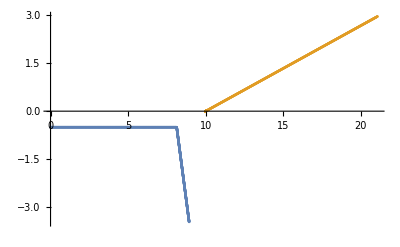

```mathematica
ListPlot[trans]
```

```mathematica
Animate[ListPolarPlot[Take[#,i]&/@rotation,PlotRange->{{-2,2},{-2,2}}],{i,1,Length[ball0],1}]
```

```mathematica
UnitConvert[Quantity[-0.22195908182356255, "Radians"], "AngularDegrees"]
```

-12.7173 °